```mathematica
2-2
```

0

```mathematica
Needs["GraphUtilities`"];
```

```mathematica
Subscript[R, effective][i_,j_]:=Γ⟦i⟧⟦i⟧+Γ⟦j⟧⟦j⟧-2Γ⟦i⟧⟦j⟧
```

# Construction of Connected Random Graphs

Nicholas Wheeler
16 November 2011

### Introduction

In "Percolation Experiments 1 & 2" I attempted to address the question: How does mean internodal resistance respond when the number of resistors (edges) in a random n-node circuit (graph) is increased, from zero to the saturation value △= n(n-1)/2 ? Using the Klein-Randić method to compute internodal resistances for large samples of such random matrices, I was led to "percolation curves" of the following form:

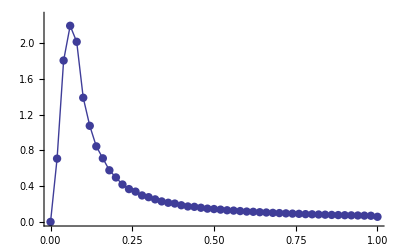

Which presented a problem? In the complete absence of resistors the averaged internodal resistance should be infinite, not zero!

Only belatedly did I realize that the Klein-Randić method purports to work only for complete graphs, and that the small-p sector of my calculation violated that condition: graphs with only few edges are typically incomplete, and are inevitably incomplete if

number of resistors < n-1

I will be making essential use later of these definitions:

```mathematica
r[p_]:=Which[0<x<p,1,p<x<1,0]/.x->RandomReal[]
```

```mathematica
𝔸[p_]:=Table[Join[Table[0,{k,1,n}],
Table[r[p],{k,1,20-n}]],{n,1,20}]
```

Here it has been assumed that 𝔸 is 20 × 20; an obvious adjustment changes the dimension of 𝔸.

### Some general observations

Assuming always that all resistors are unit resistors, and that no more than one resistor is allowed to connect a given pair of nodes…the maximal finite resistance on an n-node graph is

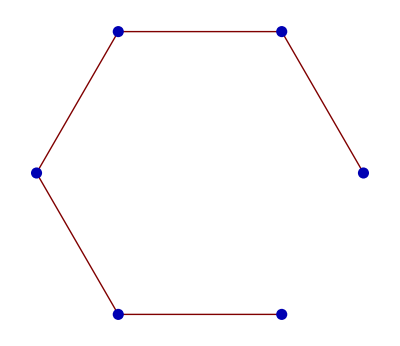

```mathematica
GraphPlot[({{0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0}}), PlotStyle->PointSize[0.02],Method->"CircularEmbedding"]
```

```mathematica
Subscript[R, max][n_]:=n-1
```

while the minimal resistance—which requires a complete graph

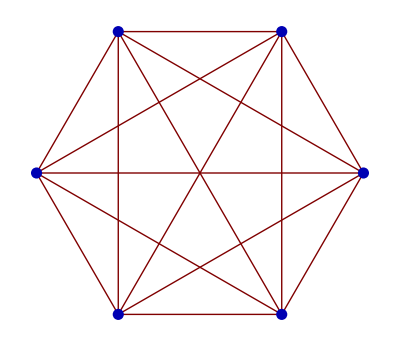

```mathematica
GraphPlot[({{0, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0}}), PlotStyle->PointSize[0.02],Method->"CircularEmbedding"]
```

—has been shown elsewhere ("Resistors on Complete Graphs.nb", 15 November 2011) to be

```mathematica
Subscript[R, min][n_]:=2/n
```

Here I display the n-dependence of those functions:

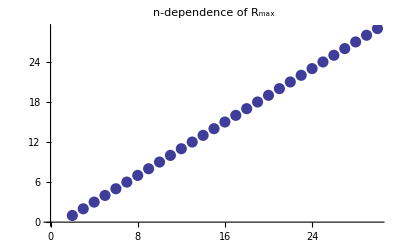

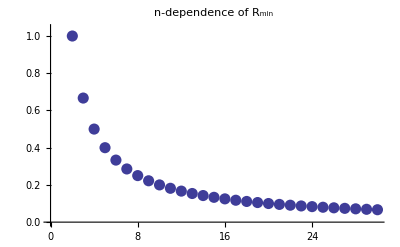

```mathematica
ListPlot[Join[{Null},Table[Subscript[R, max][n],{n,2,30}]],PlotStyle->PointSize[0.02],PlotLabel->"n-dependence of R_max"]
ListPlot[Join[{Null},Table[Subscript[R, min][n],{n,2,30}]],PlotRange->{0,1.04},PlotStyle->PointSize[0.02],PlotLabel->"n-dependence of R_min"]
```

The (n-1) edges that are required to create a minimally-connected n-node graph can be linked up in (n-1)! ways:

One can identify the set of all n-node graphs (no self-connections, no more than one link between any nodal pair) with the set of n × n matrices

```mathematica
({{0, □, □, □, □, □}, {0, 0, □, □, □, □}, {0, 0, 0, □, □, □}, {0, 0, 0, 0, □, □}, {0, 0, 0, 0, 0, □}, {0, 0, 0, 0, 0, 0}})
```

in which 0 else 1 are inserted into the □s in all possible ways. The number of □s is the triangular number

```mathematica
Δ[n_]:=1/2 n(n-1)
```

so the total number of n-node graphs is

```mathematica
TotalGraphs[n_]:=2^Δ[n]
```

which grows very rapidly:

```mathematica
Table[{n,TotalGraphs[n]},{n,2,10}]//TableForm
```

2 | 2
3 | 8
4 | 64
5 | 1024
6 | 32768
7 | 2097152
8 | 268435456
9 | 68719476736
10 | 35184372088832

A collection of m resistors can be deposited on an n-node array (graph) in this many ways:

```mathematica
SubtotalGraphs[n_,m_]:=Binomial[Δ[n],m]
```

Connectivity requires

n-1≤m≤Δ[n]

—requires, that is to say, optimal use of at least n-1 resistors.

```mathematica
Table[SubtotalGraphs[3,m],{m,2,Δ[3]}]
Table[SubtotalGraphs[4,m],{m,3,Δ[4]}]
Table[SubtotalGraphs[5,m],{m,4,Δ[5]}]
Table[SubtotalGraphs[6,m],{m,5,Δ[6]}]
```

{3,1}

{20,15,6,1}

{210,252,210,120,45,10,1}

{3003,5005,6435,6435,5005,3003,1365,455,105,15,1}

The number of possible subgraphs becomes maximal at 1/2 Δ[n]. In the case n = 6, where
Δ[6] = 15, we have the following figure:

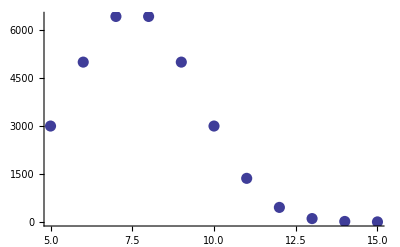

```mathematica
Table[{m,SubtotalGraphs[6,m]},{m,5,Δ[6]}];
ListPlot[%,PlotStyle->PointSize[0.02],AxesOrigin->{0,0}]
```

It is clear that n does not have to be very large for it to become no longer feasible to contemplate complete populations of graphs. Sampling procedures of some sort will have to be devised. There are, however, lessons to be learned from surveys of complete populations when n is small.

### 3-node graphs

This is the smallest not-quite-trivial case. I discuss it in detail to illustrate some methodological points which will acquire increasing importance as n becomes larger (but will seem extravagant in this instance), and to provide a context within which to formulate an interpretive distinction.

#### Case m = 0

This is trivial by any measure.

#### Case m = 1

The "connection matrices" are

```mathematica
({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}),({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})
```

which give

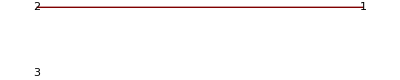

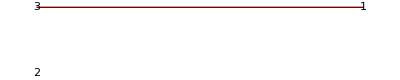

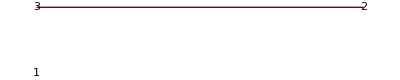

```mathematica
Subscript[g31, 1]=GraphPlot[({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}),VertexLabeling->True]
Subscript[g31, 2]=GraphPlot[({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}}),VertexLabeling->True]
Subscript[g31, 3]=GraphPlot[({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),VertexLabeling->True]
```

Those three graphs are permutationally equivalent, but give unequal readings if we suppose that our ohmmeter is attached always to (say) nodes #1 and #2. Each is a disconnected graph, so a graph to which the Klein-Randić method does not pertain: its application in the latter instance leads to a result

```mathematica
𝔸=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})+Transpose[({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,3}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,3},{j,1,3}];
𝕎//MatrixForm
```

(0. | 0.25 | 0.25
0.25 | 0. | 1.
0.25 | 1. | 0.)

which is incorrect, but which differs from the correct internodal resistance matrix

```mathematica
({{0, ∞, ∞}, {∞, 0, 1}, {∞, 1, 0}})
```

in a patterned way. One would have to dig into the bowels of the PseudoInverse construction to discover how K-R came up with that

```mathematica
1/4//N
```

0.25

It is possible but meaningless to construct (as in work cited in my Introduction I allowed myself to do)

```mathematica
"K-R mean internodal resistance"=(0.25+0.25+1.0)/3
```

and impossible to assign finite meaning to the "correct"

```mathematica
"mean internodal resistance"=(∞+∞+1.0)/3
```

#### Case m = 2

The connection matrices are

```mathematica
({{0, 1, 1}, {0, 0, 0}, {0, 0, 0}}),({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 1}, {0, 0, 1}, {0, 0, 0}})
```

which give

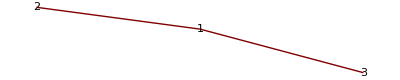

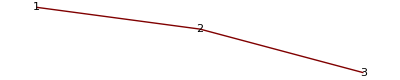

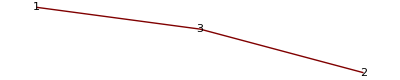

```mathematica
Subscript[g32, 1]=GraphPlot[({{0, 1, 1}, {0, 0, 0}, {0, 0, 0}}),VertexLabeling->True]
Subscript[g32, 2]=GraphPlot[({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}),VertexLabeling->True]
Subscript[g32, 3]=GraphPlot[({{0, 0, 1}, {0, 0, 1}, {0, 0, 0}}),VertexLabeling->True]
```

Those three graphs are again permutationally equivalent, and again give unequal readings if we suppose that our ohmmeter is attached always to (say) nodes #1 and #2. Each is now a connected graph, a graph to which the Klein - Randić method now does pertain : its application in the latter instance leads to a result

```mathematica
𝔸=({{0, 0, 1}, {0, 0, 1}, {0, 0, 0}})+Transpose[({{0, 0, 1}, {0, 0, 1}, {0, 0, 0}})];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,3}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,3},{j,1,3}];
𝕎//MatrixForm
```

(0. | 2. | 1.
2. | 0. | 1.
1. | 1. | 0.)

which clearly is correct.

#### Case m = 3

The solitary connection matrix in this "saturated" case is

```mathematica
({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}})
```

which supplies

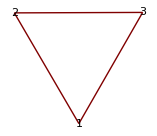

```mathematica
GraphPlot[({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}}),VertexLabeling->True]
```

```mathematica
𝔸=({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}})+Transpose[({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}})];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,3}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,3},{j,1,3}];
𝕎//MatrixForm
```

(0. | 0.666667 | 0.666667
0.666667 | 0. | 0.666667
0.666667 | 0.666667 | 0.)

which by

```mathematica
(1/1+1/2)^-1//N
```

0.666667

is seen to be precisely correct.

### 4-node graphs

When one looks to all the graphs in which m is set to the minimal value that makes connectivity possible one finds that some graphs are connected but some are not. To illustrate the point I look to the smallest non-trivial case n = 4, m =3. The number of subgraphs in this instance is

```mathematica
SubtotalGraphs[4,3]
```

20

To assemble the relevant connection matrices

𝕄=(0 | □ | □ | □
0 | 0 | □ | □
0 | 0 | 0 | □
0 | 0 | 0 | 0)

I construct 20 lists or 0s and 1s

```mathematica
P4=Permutations[{1,1,1,0,0,0}]
Length[%]
```

{{1,1,1,0,0,0},{1,1,0,1,0,0},{1,1,0,0,1,0},{1,1,0,0,0,1},{1,0,1,1,0,0},{1,0,1,0,1,0},{1,0,1,0,0,1},{1,0,0,1,1,0},{1,0,0,1,0,1},{1,0,0,0,1,1},{0,1,1,1,0,0},{0,1,1,0,1,0},{0,1,1,0,0,1},{0,1,0,1,1,0},{0,1,0,1,0,1},{0,1,0,0,1,1},{0,0,1,1,1,0},{0,0,1,1,0,1},{0,0,1,0,1,1},{0,0,0,1,1,1}}

20

from which I snip segments—thus

```mathematica
{1,0,1,0,0,1}⟹{1,0,1}+{0,0}+{1}
```

—that I used to fill in the successive rows of □s in 𝕄. By this means, I construct a 20-member list of such connection matrices

```mathematica
Table[Subscript[𝕄4, k]={Join[{0},Part[P4⟦k⟧,1;;3]],
Join[{0,0},Part[P4⟦k⟧,4;;5]],
Join[{0,0,0},Part[P4⟦k⟧,6;;6]],
{0,0,0,0}},{k,1,20}];
```

and draw the resulting graphs:

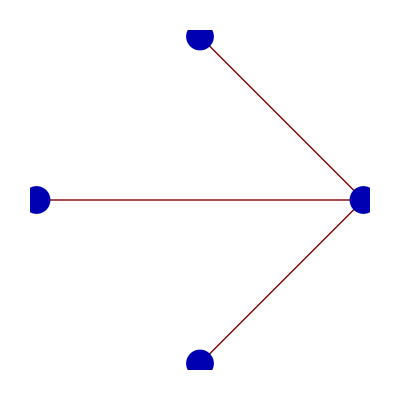
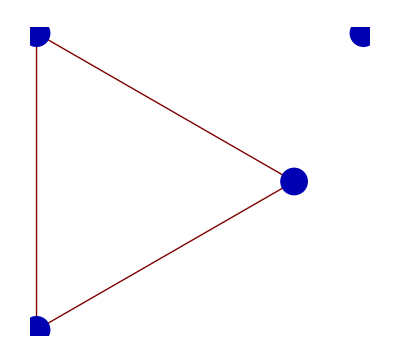
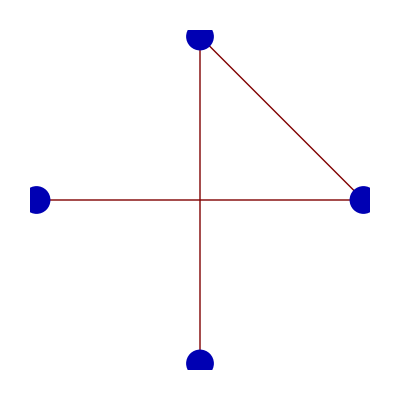
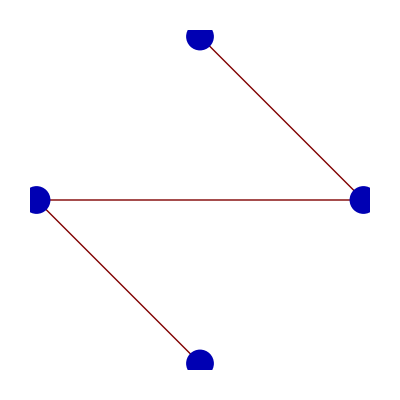
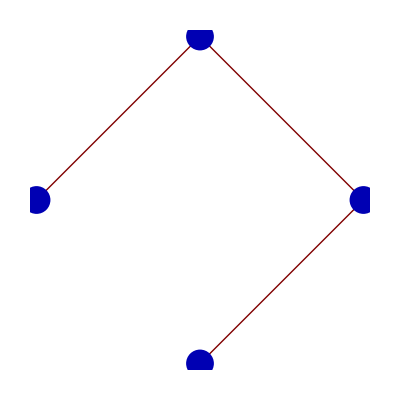
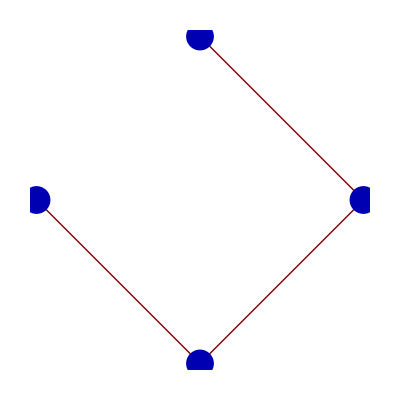
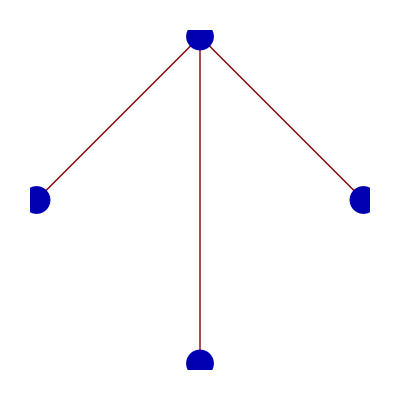
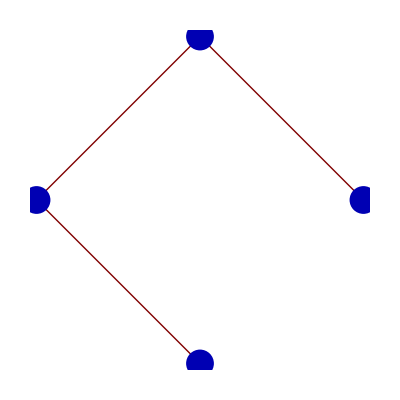
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14 | -Graphics-
15 | -Graphics-
16 | -Graphics-
17 | -Graphics-
18 | -Graphics-
19 | -Graphics-
20 | -Graphics-

```mathematica
Table[{k,GraphPlot[Subscript[𝕄4, k],PlotStyle->PointSize[0.05],Method->"CircularEmbedding"]},{k,1,20}]//TableForm
```

We see that the following four matrices give rise to disconnected graphs

```mathematica
Subscript[𝕄4, 2]//MatrixForm
Subscript[𝕄4, 6]//MatrixForm
Subscript[𝕄4, 13]//MatrixForm
Subscript[𝕄4, 20]//MatrixForm
```

(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 1 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

and that all the other 𝕄4-matrices produce connected graphs. 

The four disconnected cases are permutationally equivalent, and when subjected (misguidedly) to K-R analysis give rise to the same pattern of error: K-R consistently writes 0.222222 where it should write ∞.  I note in this connection that

```mathematica
ContinuedFraction[.22222222,4]
```

{0,4,1,1}

leads to the construction

```mathematica
1/(4+1/(1+1))
%//N
```

2/9

0.222222

Again, one would have to dig into the bowels of the  PseudoInverse  to discover how K-R came up with that 2/9.

#### Case n = 4, m = 4

Proceding as before, we construct

```mathematica
P44=Permutations[{1,1,1,1,0,0}]
Length[%]
```

{{1,1,1,1,0,0},{1,1,1,0,1,0},{1,1,1,0,0,1},{1,1,0,1,1,0},{1,1,0,1,0,1},{1,1,0,0,1,1},{1,0,1,1,1,0},{1,0,1,1,0,1},{1,0,1,0,1,1},{1,0,0,1,1,1},{0,1,1,1,1,0},{0,1,1,1,0,1},{0,1,1,0,1,1},{0,1,0,1,1,1},{0,0,1,1,1,1}}

15

```mathematica
Table[Subscript[𝕄44, k]={Join[{0},Part[P44⟦k⟧,1;;3]],
Join[{0,0},Part[P44⟦k⟧,4;;5]],
Join[{0,0,0},Part[P44⟦k⟧,6;;6]],
{0,0,0,0}},{k,1,15}];
```

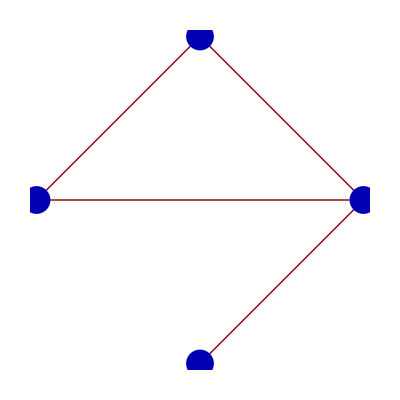
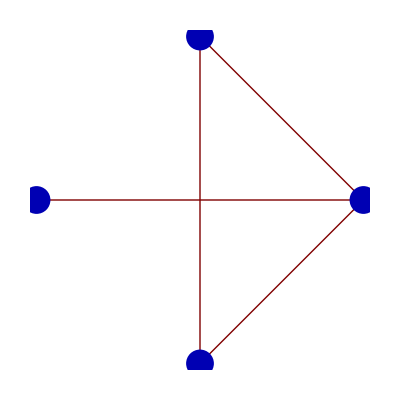
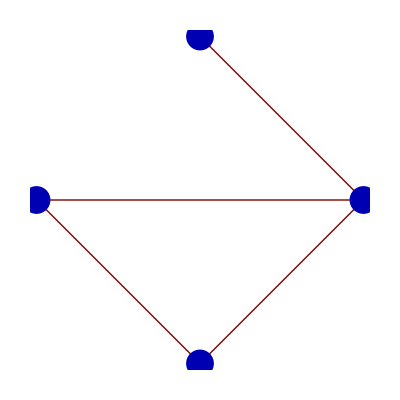
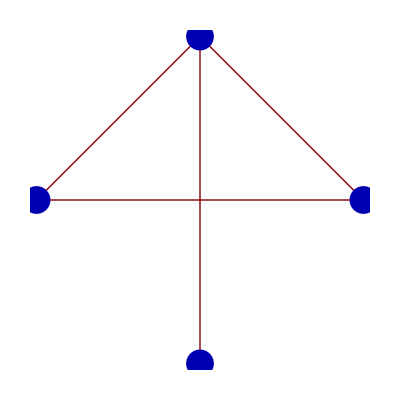
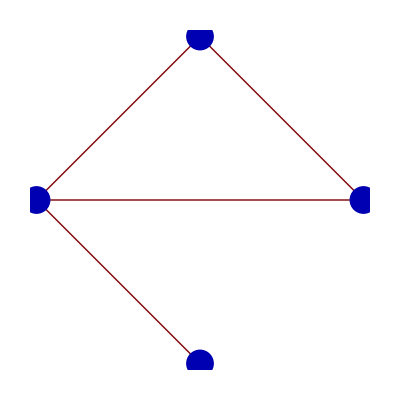
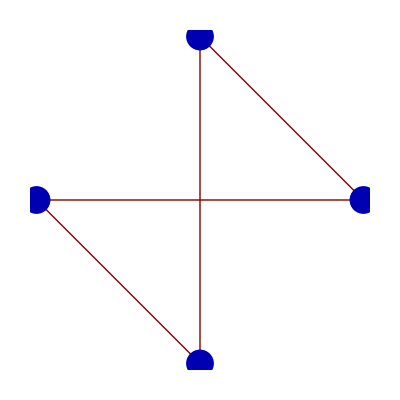
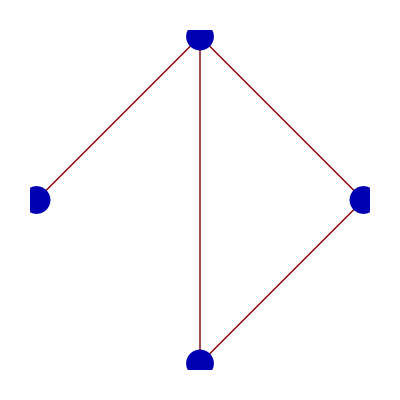
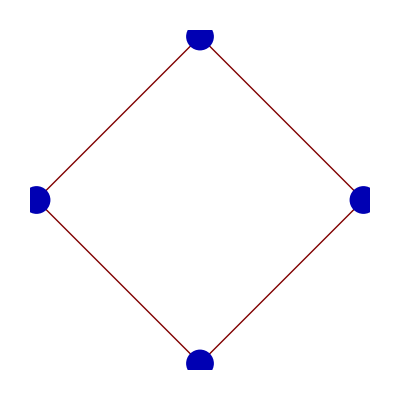
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14 | -Graphics-
15 | -Graphics-

```mathematica
Table[{k,GraphPlot[Subscript[𝕄44, k],PlotStyle->PointSize[0.05],Method->"CircularEmbedding"]},{k,1,15}]//TableForm
```

and observe that all of those graphs are connected. They are of only four distinct types:

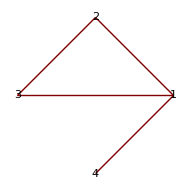

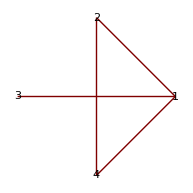

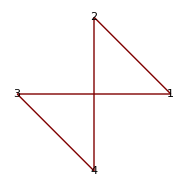

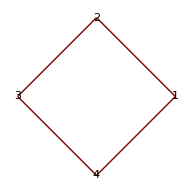

```mathematica
GraphPlot[Subscript[𝕄44, 1],VertexLabeling->True,Method->"CircularEmbedding"]
GraphPlot[Subscript[𝕄44, 2],VertexLabeling->True,Method->"CircularEmbedding"]
GraphPlot[Subscript[𝕄44, 6],VertexLabeling->True,Method->"CircularEmbedding"]
GraphPlot[Subscript[𝕄44, 8],VertexLabeling->True,Method->"CircularEmbedding"]
```

Those 4 designs are found …

```mathematica
𝔸=Subscript[𝕄44, 1]+Transpose[Subscript[𝕄44, 1]];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,4}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,4},{j,1,4}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[4])

𝔸=Subscript[𝕄44, 2]+Transpose[Subscript[𝕄44, 2]];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,4}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,4},{j,1,4}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[4])

𝔸=Subscript[𝕄44, 6]+Transpose[Subscript[𝕄44, 6]];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,4}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,4},{j,1,4}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[4])

𝔸=Subscript[𝕄44, 8]+Transpose[Subscript[𝕄44, 8]];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,4}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,4},{j,1,4}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[4])
```

(0. | 0.666667 | 0.666667 | 1.
0.666667 | 0. | 0.666667 | 1.66667
0.666667 | 0.666667 | 0. | 1.66667
1. | 1.66667 | 1.66667 | 0.)

1.05556

(0. | 0.666667 | 1. | 0.666667
0.666667 | 0. | 1.66667 | 0.666667
1. | 1.66667 | 0. | 1.66667
0.666667 | 0.666667 | 1.66667 | 0.)

1.05556

(0. | 0.75 | 0.75 | 1.
0.75 | 0. | 1. | 0.75
0.75 | 1. | 0. | 0.75
1. | 0.75 | 0.75 | 0.)

0.833333

(0. | 0.75 | 1. | 0.75
0.75 | 0. | 0.75 | 1.
1. | 0.75 | 0. | 0.75
0.75 | 1. | 0.75 | 0.)

0.833333

```mathematica
Total[Flatten[𝕎]]/(2Δ[4])
```

1.05556

…to give rise to internodal resistance matrices of only two basic types. The "mean internodal resistances" associated with those two types are found to be distinct.

#### Cases n = 4, m = 5 & 6

The graphs look like this:

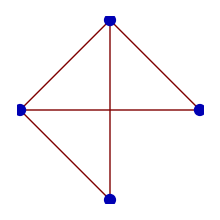

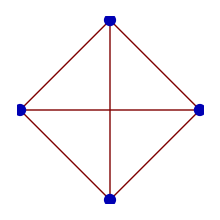

```mathematica
GraphPlot[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0, 0, 0, 0}}), PlotStyle->PointSize[0.04],Method->"CircularEmbedding"]
GraphPlot[({{0, 1, 1, 1}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0, 0, 0, 0}}), PlotStyle->PointSize[0.04],Method->"CircularEmbedding"]
```

Both are connected. I omit further discussion.

### 5-node graphs

There are, as previously remarked,

```mathematica
TotalGraphs[5]
```

1024

such graphs, so exhaustive discussion—besides being relatively pointless—is pretty much out of the question. For m < 4 all graphs are disconnected, and it becomes impossible to speak of the mean internodal resistance (it is invariably ∞). I begin, therefore, with the least value of m for which connectedness is possible, if by no means inevitable:

#### Case n = 5, m = 4

We confront now a population of

```mathematica
SubtotalGraphs[5,4]
```

210

graphs, of which many will differ only permutationally from others. Reminding ourselves that

```mathematica
Δ[5]
```

10

we use

```mathematica
P54=Permutations[{1,1,1,1,0,0,0,0,0,0}];
Length[P54]
```

210

to proceed as before to the construction of 210 connection matrices and the associated graphs:

```mathematica
Table[Subscript[𝕄54, k]={Join[{0},Part[P54⟦k⟧,1;;4]],
Join[{0,0},Part[P54⟦k⟧,5;;7]],
Join[{0,0,0},Part[P54⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P54⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,210}];
```

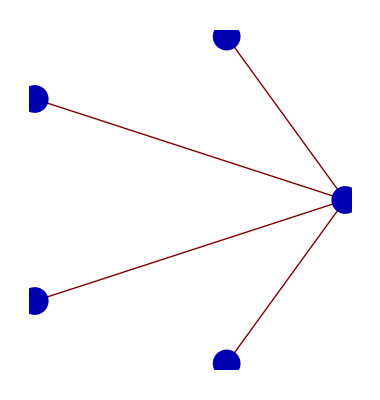
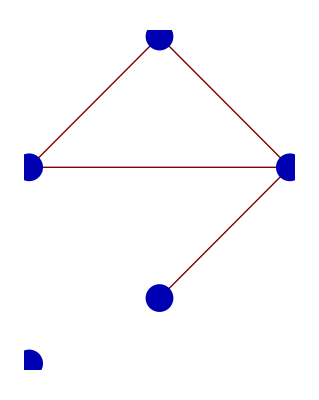
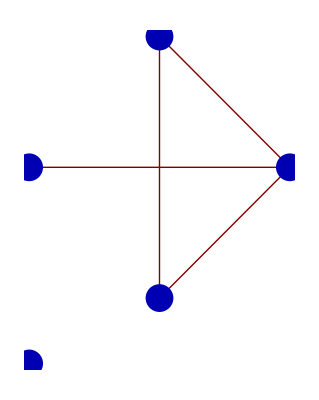
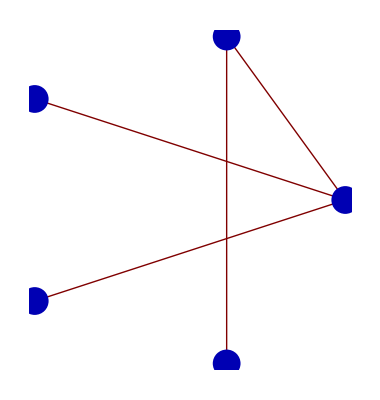
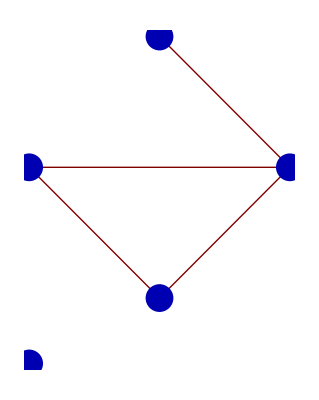
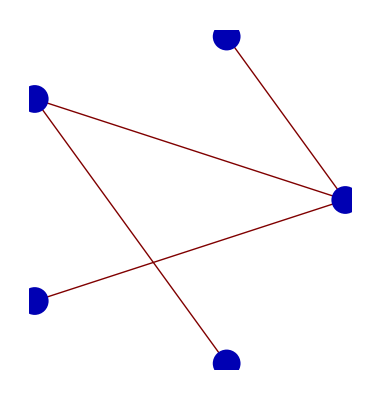
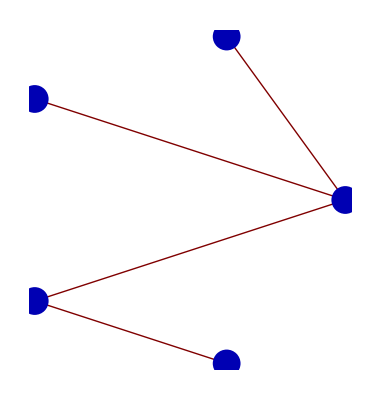
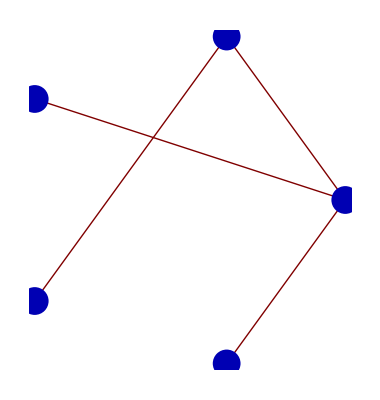
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14 | -Graphics-
15 | -Graphics-
16 | -Graphics-
17 | -Graphics-
18 | -Graphics-
19 | -Graphics-
20 | -Graphics-
21 | -Graphics-
22 | -Graphics-
23 | -Graphics-
24 | -Graphics-
25 | -Graphics-
26 | -Graphics-
27 | -Graphics-
28 | -Graphics-
29 | -Graphics-
30 | -Graphics-
31 | -Graphics-
32 | -Graphics-
33 | -Graphics-
34 | -Graphics-
35 | -Graphics-
36 | -Graphics-
37 | -Graphics-
38 | -Graphics-
39 | -Graphics-
40 | -Graphics-
41 | -Graphics-
42 | -Graphics-
43 | -Graphics-
44 | -Graphics-
45 | -Graphics-
46 | -Graphics-
47 | -Graphics-
48 | -Graphics-
49 | -Graphics-
50 | -Graphics-
51 | -Graphics-
52 | -Graphics-
53 | -Graphics-
54 | -Graphics-
55 | -Graphics-
56 | -Graphics-
57 | -Graphics-
58 | -Graphics-
59 | -Graphics-
60 | -Graphics-
61 | -Graphics-
62 | -Graphics-
63 | -Graphics-
64 | -Graphics-
65 | -Graphics-
66 | -Graphics-
67 | -Graphics-
68 | -Graphics-
69 | -Graphics-
70 | -Graphics-
71 | -Graphics-
72 | -Graphics-
73 | -Graphics-
74 | -Graphics-
75 | -Graphics-
76 | -Graphics-
77 | -Graphics-
78 | -Graphics-
79 | -Graphics-
80 | -Graphics-
81 | -Graphics-
82 | -Graphics-
83 | -Graphics-
84 | -Graphics-
85 | -Graphics-
86 | -Graphics-
87 | -Graphics-
88 | -Graphics-
89 | -Graphics-
90 | -Graphics-
91 | -Graphics-
92 | -Graphics-
93 | -Graphics-
94 | -Graphics-
95 | -Graphics-
96 | -Graphics-
97 | -Graphics-
98 | -Graphics-
99 | -Graphics-
100 | -Graphics-
101 | -Graphics-
102 | -Graphics-
103 | -Graphics-
104 | -Graphics-
105 | -Graphics-
106 | -Graphics-
107 | -Graphics-
108 | -Graphics-
109 | -Graphics-
110 | -Graphics-
111 | -Graphics-
112 | -Graphics-
113 | -Graphics-
114 | -Graphics-
115 | -Graphics-
116 | -Graphics-
117 | -Graphics-
118 | -Graphics-
119 | -Graphics-
120 | -Graphics-
121 | -Graphics-
122 | -Graphics-
123 | -Graphics-
124 | -Graphics-
125 | -Graphics-
126 | -Graphics-
127 | -Graphics-
128 | -Graphics-
129 | -Graphics-
130 | -Graphics-
131 | -Graphics-
132 | -Graphics-
133 | -Graphics-
134 | -Graphics-
135 | -Graphics-
136 | -Graphics-
137 | -Graphics-
138 | -Graphics-
139 | -Graphics-
140 | -Graphics-
141 | -Graphics-
142 | -Graphics-
143 | -Graphics-
144 | -Graphics-
145 | -Graphics-
146 | -Graphics-
147 | -Graphics-
148 | -Graphics-
149 | -Graphics-
150 | -Graphics-
151 | -Graphics-
152 | -Graphics-
153 | -Graphics-
154 | -Graphics-
155 | -Graphics-
156 | -Graphics-
157 | -Graphics-
158 | -Graphics-
159 | -Graphics-
160 | -Graphics-
161 | -Graphics-
162 | -Graphics-
163 | -Graphics-
164 | -Graphics-
165 | -Graphics-
166 | -Graphics-
167 | -Graphics-
168 | -Graphics-
169 | -Graphics-
170 | -Graphics-
171 | -Graphics-
172 | -Graphics-
173 | -Graphics-
174 | -Graphics-
175 | -Graphics-
176 | -Graphics-
177 | -Graphics-
178 | -Graphics-
179 | -Graphics-
180 | -Graphics-
181 | -Graphics-
182 | -Graphics-
183 | -Graphics-
184 | -Graphics-
185 | -Graphics-
186 | -Graphics-
187 | -Graphics-
188 | -Graphics-
189 | -Graphics-
190 | -Graphics-
191 | -Graphics-
192 | -Graphics-
193 | -Graphics-
194 | -Graphics-
195 | -Graphics-
196 | -Graphics-
197 | -Graphics-
198 | -Graphics-
199 | -Graphics-
200 | -Graphics-
201 | -Graphics-
202 | -Graphics-
203 | -Graphics-
204 | -Graphics-
205 | -Graphics-
206 | -Graphics-
207 | -Graphics-
208 | -Graphics-
209 | -Graphics-
210 | -Graphics-

```mathematica
Table[{k,GraphPlot[Subscript[𝕄54, k],PlotStyle->PointSize[0.05],Method->"CircularEmbedding"]},{k,1,210}]//TableForm
```

I have—by tedious hand counting—determined that 85 of those graphs are disconnected (all of those are in fact binary) and the rest (125) connected. There is, however, a better way to go: The commands

```mathematica
WeakComponents[Subscript[𝕄54, 1]]
WeakComponents[Subscript[𝕄54, 2]]
```

{{1,2,3,4,5}}

{{1,2,3,4},{5}}

inform us (as the eye confirms) that graph #1 is connected, #2 is binary (∴ disconnected).

```mathematica
Table[Length[WeakComponents[Subscript[𝕄54, k]]],{k,1,210}];
Count[%,2]
```

85

By this count, slightly more

```mathematica
85/210//N
```

0.404762

than 40% of the graphs in question are disconnected.

I look now to a couple of especially simple connected graphs, and observe that in both cases the computed internodal resistances are obviously correct. Observe also that in this first example the correctly averaged internodal resistance

Total[Flatten[𝕎]]/(2Δ[5])

differs markedly from the approximation

Mean[DeleteDuplicates[Flatten[𝕎]]]

that I used in previous work…this because   DeleteDuplicates command removes—in addition to all but one of the 0s on the diagonal—all but one of such off-diagonal resistances that happen to be repeated.

```mathematica
𝔾=Subscript[𝕄54, 1];
GraphPlot[𝔾,VertexLabeling->True,Method->"CircularEmbedding"]
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[5])
Mean[DeleteDuplicates[Flatten[𝕎]]]
```

-Graphics-

(0. | 1. | 1. | 1. | 1.
1. | 0. | 2. | 2. | 2.
1. | 2. | 0. | 2. | 2.
1. | 2. | 2. | 0. | 2.
1. | 2. | 2. | 2. | 0.)

1.6

1.28571

In this next example the commands

Total[Flatten[𝕎]]/(2Δ[5])
Mean[DeleteDuplicates[Flatten[𝕎]]]

happen—fortuitously—to give the same result:

```mathematica
𝔾=Subscript[𝕄54, 73];
GraphPlot[𝔾,VertexLabeling->True,Method->"CircularEmbedding"]
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[5])
Mean[DeleteDuplicates[Flatten[𝕎]]]
```

-Graphics-

(0. | 1. | 2. | 3. | 4.
1. | 0. | 1. | 2. | 3.
2. | 1. | 0. | 1. | 2.
3. | 2. | 1. | 0. | 1.
4. | 3. | 2. | 1. | 0.)

2.

2.

The Klein-Randić method, when applied to the following "irregular" connected graph, gives internodal resistances which are again obviously correct:

```mathematica
𝔾=Subscript[𝕄54, 187];
GraphPlot[𝔾,VertexLabeling->True,Method->"CircularEmbedding"]
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}];
𝕎//MatrixForm
Total[Flatten[𝕎]]/(2Δ[5])
Mean[DeleteDuplicates[Flatten[𝕎]]]
```

-Graphics-

(0. | 2. | 2. | 3. | 1.
2. | 0. | 2. | 1. | 1.
2. | 2. | 0. | 3. | 1.
3. | 1. | 3. | 0. | 2.
1. | 1. | 1. | 2. | 0.)

1.8

1.75

The Klein-Randić method clearly speaks nonsense, however, when brought to bear disconnected graphs such as the following:

```mathematica
𝔾=Subscript[𝕄54, 42];
GraphPlot[𝔾,VertexLabeling->True,Method->"CircularEmbedding"]
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,5}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,5},{j,1,5}];
Subscript[𝕎, KRdisconnected]=MatrixForm[𝕎]
```

-Graphics-

(0. | 0.666667 | 0.472222 | 0.666667 | 0.472222
0.666667 | 0. | 0.472222 | 0.666667 | 0.472222
0.472222 | 0.472222 | 0. | 0.472222 | 1.
0.666667 | 0.666667 | 0.472222 | 0. | 0.472222
0.472222 | 0.472222 | 1. | 0.472222 | 0.)

Elementary analysis indicates that the correct result in this instance reads

```mathematica
Subscript[𝕎, correct]=({{0, 2/3, ∞, 2/3, ∞}, {2/3, 0, ∞, 2/3, ∞}, {∞, ∞, 0, ∞, 1}, {2/3, 2/3, ∞, 0, ∞}, {∞, ∞, 1, ∞, 0}})//N//MatrixForm
```

(0. | 0.666667 | ∞ | 0.666667 | ∞
0.666667 | 0. | ∞ | 0.666667 | ∞
∞ | ∞ | 0. | ∞ | 1.
0.666667 | 0.666667 | ∞ | 0. | ∞
∞ | ∞ | 1. | ∞ | 0.)

When the Klein-Randić method is applied to connected fragments of the graph it again supplies correct results, as I demonstrate:

```mathematica
𝔾=({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}});
GraphPlot[𝔾,VertexLabeling->True,Method->"CircularEmbedding"]
𝔸=𝔾+Transpose[𝔾];
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,3}]];
𝕃=𝔻-𝔸;
Γ=PseudoInverse[N[𝕃]];𝕎=Table[Subscript[R, effective][i,j],{i,1,3},{j,1,3}];
𝕎//MatrixForm
```

-Graphics-

(0. | 0.666667 | 0.666667
0.666667 | 0. | 0.666667
0.666667 | 0.666667 | 0.)

Comparison of

```mathematica
Subscript[𝕎, disconnected]
```

(0. | 0.666667 | 0.472222 | 0.666667 | 0.472222
0.666667 | 0. | 0.472222 | 0.666667 | 0.472222
0.472222 | 0.472222 | 0. | 0.472222 | 1.
0.666667 | 0.666667 | 0.472222 | 0. | 0.472222
0.472222 | 0.472222 | 1. | 0.472222 | 0.)

and

```mathematica
Subscript[𝕎, correct]
```

(0. | 0.666667 | ∞ | 0.666667 | ∞
0.666667 | 0. | ∞ | 0.666667 | ∞
∞ | ∞ | 0. | ∞ | 1.
0.666667 | 0.666667 | ∞ | 0. | ∞
∞ | ∞ | 1. | ∞ | 0.)

we see that the errors in the former conform to a very simple and regular pattern: teh K-R method has systematically written 0.472222 where it should have written ∞, and in all other particulars is correct.

Drawing again uon a procedure employed already once before, we command

```mathematica
ContinuedFraction[.472222222,4]
```

{0,2,8,2}

to obtain

```mathematica
1/(2+1/(8+1/2))
```

17/36

```mathematica
N[%,10]
```

0.4722222222

### Increasing likelihood of connectedness

We have seen that, for a 5-node graph, connectedness—impossible if m < 4—stands already at

```mathematica
125/210 100//N
```

59.5238

% as soon as it becomes possible (at m = 5). We expect it to increase as m ranges upward from 5 toward,

```mathematica
Δ[5]
```

10

and ultimately to become inevitable.

```mathematica
P54=Permutations[{1,1,1,1,0,0,0,0,0,0}];

Table[Subscript[𝕄54, k]={Join[{0},Part[P54⟦k⟧,1;;4]],
Join[{0,0},Part[P54⟦k⟧,5;;7]],
Join[{0,0,0},Part[P54⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P54⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,Length[P54]}];

Table[Length[WeakComponents[Subscript[𝕄54, k]]],{k,1,Length[P54]}];
Count[%,2];

Subscript[Likelihood, 4]=100-100 %/Length[P54]//N
```

59.5238

```mathematica
P55=Permutations[{1,1,1,1,1,0,0,0,0,0}];

Table[Subscript[𝕄55, k]={Join[{0},Part[P55⟦k⟧,1;;4]],
Join[{0,0},Part[P55⟦k⟧,5;;7]],
Join[{0,0,0},Part[P55⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P55⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,Length[P55]}];

Table[Length[WeakComponents[Subscript[𝕄55, k]]],{k,1,Length[P55]}];
Count[%,2];

Subscript[Likelihood, 5]=100-100 %/Length[P55]//N
```

88.0952

```mathematica
P56=Permutations[{1,1,1,1,1,1,0,0,0,0}];

Table[Subscript[𝕄56, k]={Join[{0},Part[P56⟦k⟧,1;;4]],
Join[{0,0},Part[P56⟦k⟧,5;;7]],
Join[{0,0,0},Part[P56⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P56⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,Length[P56]}];

Table[Length[WeakComponents[Subscript[𝕄56, k]]],{k,1,Length[P56]}];
Count[%,2];

Subscript[Likelihood, 6]=100-100 %/Length[P56]//N
```

97.619

```mathematica
P57=Permutations[{1,1,1,1,1,1,1,0,0,0}];

Table[Subscript[𝕄57, k]={Join[{0},Part[P57⟦k⟧,1;;4]],
Join[{0,0},Part[P57⟦k⟧,5;;7]],
Join[{0,0,0},Part[P57⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P57⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,Length[P57]}];

Table[Length[WeakComponents[Subscript[𝕄57, k]]],{k,1,Length[P57]}];
Count[%,2];

Subscript[Likelihood, 7]=100-100 %/Length[P57]//N
```

100.

```mathematica
P58=Permutations[{1,1,1,1,1,1,1,1,0,0}];

Table[Subscript[𝕄58, k]={Join[{0},Part[P58⟦k⟧,1;;4]],
Join[{0,0},Part[P58⟦k⟧,5;;7]],
Join[{0,0,0},Part[P58⟦k⟧,8;;9]],
Join[{0,0,0,0},Part[P58⟦k⟧,10;;10]],
{0,0,0,0,0}},{k,1,Length[P58]}];

Table[Length[WeakComponents[Subscript[𝕄58, k]]],{k,1,Length[P58]}];
Count[%,2];

Subscript[Likelihood, 8]=100-100 %/Length[P58]//N
```

100.

```mathematica
ListPlot[{0,0,0,Subscript[Likelihood, 4],Subscript[Likelihood, 5],Subscript[Likelihood, 6],Subscript[Likelihood, 7],Subscript[Likelihood, 8],100,100},PlotStyle->PointSize[0.02],AxesLabel->{"m","Connectedness Likelihood"},GridLines->{{4},{100}}]
```

-Graphics-

If I had more patience/motivation I might construct a similar plot for a 10-node graph

```mathematica
Δ[10]
```

45

but—as the following table makes clear

```mathematica
Table[{m,SubtotalGraphs[10,m]},{m,9,Δ[10]}]//TableForm
```

9 | 886163135
10 | 3190187286
11 | 10150595910
12 | 28760021745
13 | 73006209045
14 | 166871334960
15 | 344867425584
16 | 646626422970
17 | 1103068603890
18 | 1715884494940
19 | 2438362177020
20 | 3169870830126
21 | 3773655750150
22 | 4116715363800
23 | 4116715363800
24 | 3773655750150
25 | 3169870830126
26 | 2438362177020
27 | 1715884494940
28 | 1103068603890
29 | 646626422970
30 | 344867425584
31 | 166871334960
32 | 73006209045
33 | 28760021745
34 | 10150595910
35 | 3190187286
36 | 886163135
37 | 215553195
38 | 45379620
39 | 8145060
40 | 1221759
41 | 148995
42 | 14190
43 | 990
44 | 45
45 | 1

—one would have to forego exhaustive enumeration, would have to resort to some kind of fair sampling procedure. 

Here I have examined the case

```mathematica
Table[{m,SubtotalGraphs[5,m]},{m,4,Δ[5]}]//TableForm
```

4 | 210
5 | 252
6 | 210
7 | 120
8 | 45
9 | 10
10 | 1

It is remarkable that such a small adjustment as 5⟶10 can turn a tractable problem into a monster. But compare

```mathematica
2^Δ[5]
2^Δ[10]
```

1024

35184372088832

The adjustment 5⟶10 inflates the problem by the following factor:

```mathematica
2^Δ[10]/2^Δ[5]
```

34359738368

```mathematica
2^(Δ[10]-Δ[5])
```

34359738368

### Development of a "connectedness filter"

If I am, for the reason just touched upon, forced to construct my connection matrices (graphs) not by exhaustive enumeration but randomly, then I will stand in need of means to discard unconnected graphs. To that end I introduce a command

```mathematica
CompletenessFilter[M_]:=If[Length[WeakComponents[M]]≠1,0,M]
```

that is intended to accept (commection) matrices as arguments. To illustrate how this command works, I borrow from preceding work the matrices

```mathematica
Subscript[𝕄, 1]={{0,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Subscript[𝕄, 2]={{0,1,1,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}};
```

of which the first generates a connected 4-node graph, the second an unconnected graph:

```mathematica
GraphPlot[Subscript[𝕄, 1],PlotStyle->PointSize[0.05],Method->"CircularEmbedding"]
GraphPlot[Subscript[𝕄, 2],PlotStyle->PointSize[0.05],Method->"CircularEmbedding"]
```

-Graphics-

-Graphics-

The complete/uncomplete distinction is now exposed

```mathematica
CompletenessFilter[Subscript[𝕄, 1]]
CompletenessFilter[Subscript[𝕄, 2]]
```

{{0,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

0

```mathematica
CompletenessFilter[Subscript[𝕄, 1]]===Subscript[𝕄, 1]
CompletenessFilter[Subscript[𝕄, 2]]===Subscript[𝕄, 2]
```

True

False

I now reconstruct a previous list of 4-node matrices

```mathematica
P4=Permutations[{1,1,1,0,0,0}];

RawMatrixSet=Table[Subscript[𝕄4, k]={Join[{0},Part[P4⟦k⟧,1;;3]],
Join[{0,0},Part[P4⟦k⟧,4;;5]],
Join[{0,0,0},Part[P4⟦k⟧,6;;6]],
{0,0,0,0}},{k,1,20}];
```

That is a list of

```mathematica
Length[RawMatrixSet]
```

20

matrices of which we know from previous work that 4 generate unconnected graphs. The command

```mathematica
DistilledMatrixSet=Table[CompletenessFilter[RawMatrixSet⟦k⟧],{k,1,20}];
```

```mathematica
Length[DistilledMatrixSet]
```

20

converts those matrices to place-holding zeros, which the following command discards:

```mathematica
FilteredMatrixList=DeleteCases[DistilledMatrixSet,0];
```

```mathematica
Length[FilteredMatrixList]
```

16

We verify that each of the surviving matrices (elements of the filtered list) is connected:

```mathematica
Table[Length[WeakComponents[FilteredMatrixList⟦k⟧]], {k,1,Length[FilteredMatrixList]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

16

We could, by similar means, isolate bi-connected, tri-connected … graphs if we had interest in them.

### Return to the percolation problem that first motivated this work

We must be clear about (1) what it is we propose to measure (resistance vs. conductance) and (2) how we propose to conduct those measurements. In all cases, we propose to drop m unit resistors onto an n-node graph, with m ranging from 1 to Δ[n].

I illustrate the alternatives as they relate to the simplest possible non-trivial case n =  3 (m = 1, 2, 3). I use ● to indicate nodes, and ● to indicate nodes to which the ohmmeter probes are connected.

#### Fixed probe protocol

Clip the meter probes to a selected pair of nodes. Drop a resistor randomly, many times.

-Graphics-

Read R = {1, ∞, ∞} with equal frequency. Note that

R_mean[3,1]=(1+∞+∞)/3   is undefined

If, on the other hand, the meter is a conductance meter get

C_mean[3,1]=(1+0+0)/3=1/3

Now drop a 2nd resistor (many times).

-Graphics-

Read R = {1, 1, 2} with equal frequency, giving

R_mean[3,2]=(1+1+2)/3=4/3
C_mean[3,2]=(1+1+1/2)/3=5/6

Notice that each of those graphs is connected, so yields to Klein-Randić analysis.

Finally, drop a 3rd resistor:

-Graphics-

Read

```mathematica
(1/1+1/2)^-1
```

2/3

invariably, giving

R_mean[3,3]=2/3
C_mean[3,3]=3/2

#### Movable probe protocol

Connect a resistor to a selected pair of nodes. Measure all internodal resistances:

-Graphics-

Get R = {1, ∞, ∞}, giving again

R[3,1]=(1+∞+∞)/3   is undefined

C_mean[3,1]=(1+0+0)/3=1/3

Now install a 2nd resistor

-Graphics-

and measure all internodal resistances; again get R = {1, 1, 2} giving

R_mean[3,2]=(1+1+2)/3=4/3
C_mean[3,2]=(1+1+1/2)/3=5/6

Notice again that each of those graphs is connected, so yields to Klein-Randić analysis.

Finally, install the 3rd resistor

-Graphics-

and, proceeding as before, recover

R_mean[3,3]=2/3
C_mean[3,3]=3/2

The Fixed Probe Protocol requires investment in the construction of many m-resistor circuits. Exhaustive survey of the possibilities becomes impossible if n is large enough to be interesting; one must in such cases resort to statistical sampling. The K-R method can be used to evaluate

```mathematica
Subscript[R, effective][a,b]:=Γ⟦a⟧⟦a⟧+Γ⟦b⟧⟦b⟧-2Γ⟦a⟧⟦b⟧
```

only if the probe nodes a & b are members of an identifiable connected subgraph.

The Movable Probe Protocol enables one to extract maximal data from each randomly constructed m-resistor circuit. The K-R method is subject to the same limitation as before, but it permits one to evaluate and average internodal resistances in subcircuit-wide batches. 

One must, in all events, identify connected subcircuits before attempting to exploit the K-R method. This I failed to do in "Percolation Expereiments 1 & 2." For m not too small one can expect most/all randomly constructed circuits to be connected,  so one can have fair confidence in the descending tail of the figures such as the following:

-Graphics-

But when m is small the connectedness requirement is frequently violated, and the K-R method reports faulty numbers.

### Relationship between "effective conductance" and "mean conductance"

We encountered in the preceding discussion a situation

-Graphics-

that gave

R_mean[3,2]=(1+1+2)/3=4/3
C_mean[3,2]=(1+1+1/2)/3=5/6

Notice that  C_mean[3,2]≠1/R_mean[3,2], and more particularly that

C_mean[3,2]>1/R_mean[3,2]

Or—to say the same thing another way—

R_mean[3,2]>1/C_mean[3,2]

This is a particular instance of the assertion

(r_1+r_2+⋯+r_n)/n≥n 1/(1/r_1+1/r_2+⋯+1/r_n)

which—phrased

arithemetic mean ≥ harmonic mean

—is classic. See

```mathematica
Hyperlink["Inequalities","http://en.wikipedia.org/wiki/Inequality_(mathematics)"]
```

The p^th power mean

M_p[r_1,r_2,…,r_n]=(1/n∑_(i=1)^n x_i^p)^(1/p)

—see

```mathematica
Hyperlink["Power Mean","http://en.wikipedia.org/wiki/Power_mean"]
```

—gives back the arithmetic and harmonic means as special cases, and is known to give rise to the generalized inequality

```mathematica
(1/n∑_(i=1)^n Subscript[x, i]^q)^q≥(1/n∑_(i=1)^n Subscript[x, i]^p)^p   :   q > p
```

Our immediate interest attaches to the cases q = 1 > p = -1. We have

Mean Conductance ≥ Effective Conductance

with equality iff all resistances/conductances are the same.